# CS111B-How to use Mathematica

## Matrix operations

The basic representation of a matrix is a list of lists. To get the data structure in a more human-readable format, either wrap it in MatrixForm and evaluate, or mark the entire matrix, right-click, select “Convert to”, and choose “Traditional form” from the drop-down menu.

```mathematica
MatrixForm[{{1,2,3},{4,5,6},{7,3,9}}]
```

(1 | 2 | 3
4 | 5 | 6
7 | 3 | 9)

To put a matrix in RREF, use RowReduce:

```mathematica
RowReduce[({{1, 2, 3}, {4, 5, 6}, {7, 3, 9}})]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Another useful function is LinearSolve. It can be used to solve equations of the form m.x=b :

```mathematica
LinearSolve[({{1, 2, 3}, {4, 5, 6}, {7, 3, 9}}),({{1}, {4}, {8}})]//MatrixForm
```

(11/10
-1/5
1/10)

This function can also be used to get the change of basis matrix:

```mathematica
LinearSolve[({{1, 2, 3}, {4, 5, 6}, {7, 3, 9}}),({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]//MatrixForm
```

(-9/10 | 3/10 | 1/10
-1/5 | 2/5 | -1/5
23/30 | -11/30 | 1/10)

## Plotting vectors

The easiest way to plot vectors is using the ResourceFunctions PlotVector and PlotVector3D.

```mathematica
PlotVector=ResourceFunction["PlotVector"];
```

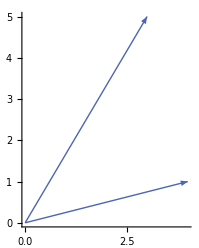

```mathematica
PlotVector[{{4,1},{3,5}}]
```

There are many ways to customizie the function

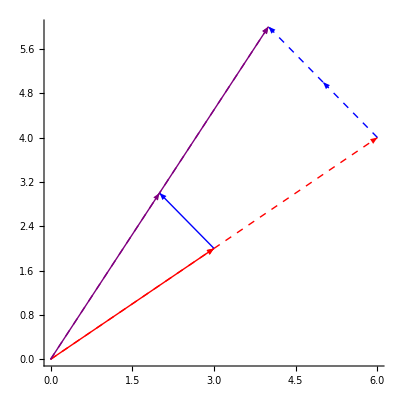

```mathematica
PlotVector[{{{3,2},{0,0}},{{3,2},{3,2}},{{-1,1},{6,4}},{{-1,1},{5,5}},{{3,2},{0,0}},{{-1,1},{3,2}},{{2,3},{0,0}},{{2,3},{2,3}},{{4,6},{0,0}}},
VectorStyle->{{Red,Dashed},{Red,Dashed},{Blue,Dashed},{Blue,Dashed},Red,Blue,Purple,Purple,{Purple,Dashed}}]
```

PlotVector3D basically works the same but with added dimensions:

```mathematica
ResourceFunction["PlotVector3D"][{{1,2,3},{3,4,2}}]
```

-Graphics3D-

## Plotting graphs

One of the biggest advantage I found in using Mathematica for CS111B was the ease of plotting graphs with Graph.

Make an undirected graph:

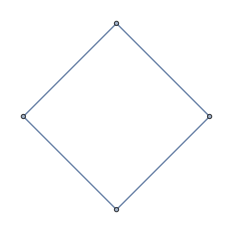

```mathematica
Graph[{1<->4,1<->2,2<->3,4<->3}]
```

Make a directed graph :

```mathematica
Graph[{1->4,1->2,2->3,4->3}]
```

-Graphics-

Add labels and styles as you want:

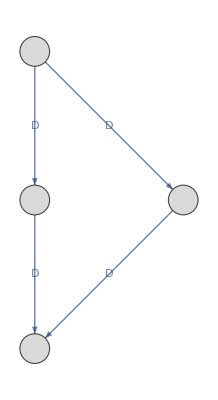

```mathematica
Graph[{1->4,1->2,2->3,4->3},VertexStyle->LightGray,VertexSize->Medium,VertexLabels->Placed[Automatic,Center],EdgeLabels->{"A","B","C","D"}]
```